```mathematica
Sum[(-1)^k/(2k+1)! x^(2k+1),{k,0,Infinity}]
```

Sin[x]

```mathematica
Sum[(-1)^k/(2k+1)! x^(2k+1)/(2k+1)!,{k,0,Infinity}]
```

KelvinBei[0,2 √x]

```mathematica
Sum[(-1)^k/(2k+1)! Binomial[x,2k+1],{k,0,Infinity}]
```

x HypergeometricPFQ[{1/2-x/2,1-x/2},{1,3/2,3/2},-1/4]

```mathematica
Sum[(-1)^k/(2k+1)! (-1)^-k Gamma[k,0,-Log[x]]/Gamma[k],{k,0,Infinity}]
```

∑_(k=0)^∞ Gamma[k,0,-Log[x]]/((1+2 k)! Gamma[k])

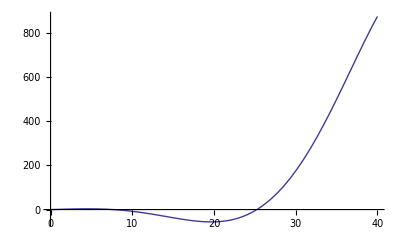

```mathematica
Plot[x HypergeometricPFQ[{1/2-x/2,1-x/2},{1,3/2,3/2},-1/4],{x,0,40}]
```

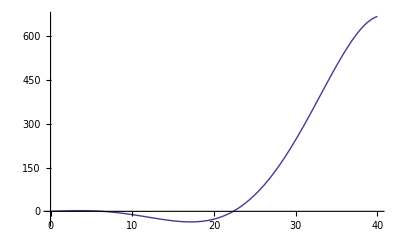

```mathematica
Plot[KelvinBei[0,2 √x],{x,0,40}]
```

```mathematica
Plot[∑_(k=0)^∞ Gamma[k,0,-Log[x]]/((1+2 k)! Gamma[k]),{x,0,40}]
```

Infinity::indet: Indeterminate expression 0.\ ∞ encountered.

Infinity::indet: Indeterminate expression 0\ ∞ encountered.

NSum::nsnum: Summand (or its derivative) Gamma[k, 0, 7.1097]/(1 + 2\ k) !\ Gamma[k] is not numerical at point k = 0.

Infinity::indet: Indeterminate expression 0.\ ∞ encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

NSum::nsnum: Summand (or its derivative) Gamma[k, 0, 7.1097]/(1 + 2\ k) !\ Gamma[k] is not numerical at point k = 0.

NSum::nsnum: Summand (or its derivative) Gamma[k, 0., 7.1097]/(1.  + 2.\ k) !\ Gamma[k]
 is not numerical at point k = 0..

General::stop: Further output of NSum :: nsnum will be suppressed during this calculation.

$Aborted

```mathematica
Integrate[1/u-E^-u/u,{u,0,x-t}]
```

ConditionalExpression[EulerGamma+Gamma[0,-t+x]+Log[-t+x],Re[t]<Re[x]]

```mathematica
Binomial[x,1]
```

x

```mathematica
(-1)^-k Gamma[k,0,-Log[x]]/Gamma[k]/.k->1
```

-1+x

```mathematica
Sum[Limit[D[t/(Log[1+t]),{t,j}],t->0]/j! x^(k+j-1) Log[1+x],{j,0,30}]/.k->1/.x->10.
```

-3.20046×10^27

```mathematica
Limit[D[t/(Log[1+t]),{t,3}],t->0]
```

1/4

```mathematica
ka[x_,a_]:=Sum[Binomial[t-1,a-1]HarmonicNumber[x-t],{t,1,x}]
ka1[x_]:=Sum[HarmonicNumber[x-t],{t,1,x}]
ka2[x_,a_]:=Sum[(-1)^(k+1)/k Binomial[x,k+a],{k,1,x}]
```

```mathematica
ka[10,0]
```

0

```mathematica
ka2[10,0]
```

7381/2520

```mathematica
ka1[10]
```

4861/252

```mathematica
Binomial[0,1]
```

0

```mathematica
Binomial[-1,0]
```

1

```mathematica
Sum[SeriesCoefficient[t/Log[1+t],{t,0,j}] x^(j-1+k) Log[1+x],{j,0,30}]/.x->.7/.k->1.5
```

0.585662

```mathematica
SeriesCoefficient[x/Log[1+x],{x,0,4}]
```

-19/720

```mathematica
Limit[D[t/(Log[1+t]),{t,4}],t->0]
```

-19/30

```mathematica
.7^1.5
```

0.585662

```mathematica
es[j_]:=es[j]=SeriesCoefficient[r/Log[1+r],{r,0,j}]
Sum[es[j]Sum[Binomial[t-1,k+j-2]HarmonicNumber[x-t],{t,1,x}],{j,0,80}]/.x->10./.k->2
```

45.

```mathematica
N@HarmonicNumber[10]+N@Sum[es[j]Sum[Binomial[t-1,j-1]HarmonicNumber[10-t],{t,1,10}],{j,0,30}]
```

10.

```mathematica
ka[x_,j_,k_]:=Integrate[t^(k+j-2)/(k+j-2)! (-ExpIntegralEi[-x+t]+Log[x-t]+EulerGamma),{t,0,x}]
```

```mathematica
ka[10,j,2]
```

∫_0^10 (t^j (EulerGamma-ExpIntegralEi[-10+t]+Log[10-t]))/(j!)ⅆt

```mathematica
Sum[es[j]ka[10.,j,2],{j,0,30}]
```

50.

```mathematica
10^2/2!
```

50

```mathematica
Sum[es[j]ka[10.,j,1],{j,0,30}]
```

7.12019

```mathematica
(-ExpIntegralEi[-x+t]+Log[x-t]+EulerGamma)/.t->0/.x->10.
```

2.8798

```mathematica
7.120194713423597+2.879804914864508
```

10.

```mathematica
ka2[x_,j_,k_]:=Integrate[Log[t]^(k+j-2)/(k+j-2)! (LogIntegral[x/t]-Log[Log[x/t]]-EulerGamma),{t,1,x}]
```

```mathematica
Sum[es[j]ka2[10.,j,1],{j,0,30}]
```

4.24565

```mathematica
LogIntegral[x/t]-Log[Log[x/t]]-EulerGamma/.t->1/.x->10.
```

4.75435

```mathematica
4.245647499125847+4.7543513946378075
```

9.

```mathematica
Log[t]^(j-1)/(j-1)!/.j->0
```

0

```mathematica
Integrate[LaguerreL[z-1,1,-t],{t,0,x}]
```

-LaguerreL[z,0]+LaguerreL[z,-x]

```mathematica
-LaguerreL[z,0]/.z->14
```

-1

```mathematica
Integrate[LaguerreL[-z-1,1,-u],{u,0,x/2}]
```

ConditionalExpression[-1+Hypergeometric1F1[z,1,-x/2],Re[x]≥-2||x∉Reals]

```mathematica
Integrate[LaguerreL[z-1,1,-t],{t,0,(x-2u)}]
```

-LaguerreL[z,0]+LaguerreL[z,2 u-x]

```mathematica
-LaguerreL[z,0]/.z->3
```

-1

```mathematica
Integrate[LaguerreL[z-1,1,-t] LaguerreL[-z-1,1,-u],{t,0,x},{u,0,(x-t)/2}]
```

∫_0^x z Hypergeometric1F1[1-z,2,-t] (-1+Hypergeometric1F1[z,1,(t-x)/2])ⅆt

```mathematica
Integrate[LaguerreL[z-1,1,-t] LaguerreL[-z-1,1,-u],{u,0,x/2},{t,0,(x-2u)}]
```

∫_0^(x/2) (-1+LaguerreL[z,2 u-x]) LaguerreL[-1-z,1,-u]ⅆu

```mathematica
Integrate[LaguerreL[-z-1,1,-Log[u]],{u,1,x^(1/2)}]
```

∫_1^(√x) LaguerreL[-1-z,1,-Log[u]]ⅆu

```mathematica
Integrate[LaguerreL[z-1,1,-Log[t]],{t,1,x}]
```

∫_1^x LaguerreL[-1+z,1,-Log[t]]ⅆt

```mathematica
FullSimplify[Sum[pex[-z,u],{u,0,a}]]/.a->3.3/.z->2.2
```

0.0243613

```mathematica
pex[-z+1,a]/.a->3.3/.z->2.2
```

0.0243613-5.9668×10^-18 ⅈ

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:= Product[(-1)^p[[2]]bin[-z,p[[2]]],{p,FI[n]}]
Dz[n_,z_]:=Sum[dz[j,z],{j,1,n}]
Di[n_,z_]:=Sum[Dz[n/u^2,z]dz[u,-z],{u,1,n^(1/2)}]
di[n_,z_]:=Di[n,z]-Di[n-1,z]
dia[n_,z_]:= Product[bin[z,p[[2]]],{p,FI[n]}]
Dia[n_,z_]:=Sum[dia[j,z],{j,1,n}]
pex[z_,u_]:=Pochhammer[z,u]/u!
pz[x_,z_]:=Sum[pex[z+1,x-2u]pex[-z,u],{u,0,x/2}]
dpz[x_,z_]:=Sum[pex[z,x-2u]pex[-z,u],{u,0,x/2}]
```

```mathematica
Expand@Di[100,z]
```

1+(116 z)/5+(9389 z^2)/360+(395 z^3)/48+(347 z^4)/144+(17 z^5)/240+(7 z^6)/720

```mathematica
Expand@pz[10,z]
```

1+(1627 z)/2520+(19013 z^2)/50400-(2729 z^3)/25920+(8161 z^4)/72576-(1339 z^5)/34560+(1753 z^6)/172800-(193 z^7)/120960+z^8/6048-z^9/103680+z^10/3628800

```mathematica
Expand@Sum[bin[z,k],{k,0,10}]
```

1+(1627 z)/2520+(19013 z^2)/50400-(2729 z^3)/25920+(8161 z^4)/72576-(1339 z^5)/34560+(1753 z^6)/172800-(193 z^7)/120960+z^8/6048-z^9/103680+z^10/3628800

```mathematica
pz[20,6.5]
```

90.5097

```mathematica
2^6.5
```

90.5097

```mathematica
mes[x_,z_]:=-1+LaguerreL[z,-x]+Hypergeometric1F1[z,1,-x/2]+Integrate[(LaguerreL[z,2u-x]-1)LaguerreL[-z-1,1,-u],{u,0,x/2}]
mesa[x_,z_]:={-1,LaguerreL[z,-x],Hypergeometric1F1[z,1,-x/2],Integrate[(LaguerreL[z,2u-x]-1)LaguerreL[-z-1,1,-u],{u,0,x/2}]}
med[x_,z_]:=1+Integrate[LaguerreL[z-1,1,-Log[t]],{t,1,x}]+Integrate[LaguerreL[-z-1,1,-Log[u]],{u,1,x^(1/2)}]+Integrate[LaguerreL[z-1,1,-Log[t]]LaguerreL[-z-1,1,-Log[u]],{t,1,x},{u,1,(x/t)^(1/2)}]
```

```mathematica
N@mes[60,-7.3+I]
```

0.0048824+0.00405638 ⅈ

```mathematica
2^(-7.3+I)
```

0.00488138+0.00405467 ⅈ

```mathematica
N@med[40.,3]
```

161.367

```mathematica
N@mesa[50,2.2]
```

{-1.,2476.78,0.000215942,-2471.18}

```mathematica
N@mes[50,2.2]
```

4.59479

```mathematica
N[D[mes[10,z],z]/.z->0]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.692003

```mathematica
N[(-ExpIntegralEi[-10]+Log[10]+EulerGamma)-(-ExpIntegralEi[-5]+Log[5]+EulerGamma)]
```

0.692003

```mathematica
N[(-ExpIntegralEi[-10])-(-ExpIntegralEi[-5])]+Log[2]
```

0.692003

```mathematica
Log[2.]
```

0.693147

```mathematica
N[D[med[10,z],z]/.z->0]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

3.16461

```mathematica
N[(LogIntegral[10]-Log[Log[10]]-EulerGamma)-((LogIntegral[10^(1/2)]-Log[Log[10^(1/2)]]-EulerGamma))]
```

3.16461

```mathematica
2^2.2
```

4.59479

```mathematica
mesk[x_,z_,k_]:=-1+LaguerreL[z,-x]+Hypergeometric1F1[z,1,-x/k]+Integrate[(LaguerreL[z,k u-x]-1)LaguerreL[-z-1,1,-u],{u,0,x/k}]
mesko[x_,z_,k_]:={-1,LaguerreL[z,-x],Hypergeometric1F1[z,1,-x/k],Integrate[(LaguerreL[z,k u-x]-1)LaguerreL[-z-1,1,-u],{u,0,x/k}]}
```

```mathematica
N@mesk[80,2.2+3I,3+I]
```

-2.50903-4.08627 ⅈ

```mathematica
(3+I)^(2.2+3I)
```

-2.50903-4.08627 ⅈ

```mathematica
pex[z_,u_]:=Pochhammer[z,u]/u!
pex2[z_,u_]:=Gamma[z+u]/Gamma[z]/Gamma[1+u]
pzk[x_,z_,k_]:=Sum[pex[z+1,x-k u]pex[-z,u],{u,0,x/k}]
```

```mathematica
N@pzk[3,1,E]
```

2.71828

```mathematica
E^(2.8+I)
```

8.88508+13.8377 ⅈ

```mathematica
(LogIntegral[n]-Log[Log[n]]-EulerGamma)-((LogIntegral[n^(1/2)]-Log[Log[n^(1/2)]]-EulerGamma))
```

Log[Log[√n]]-Log[Log[n]]-LogIntegral[√n]+LogIntegral[n]

```mathematica
FullSimplify[Log[Log[√n]]-Log[Log[n]]]
```

-Log[2]

```mathematica
FullSimplify[Log[n]-Log[n/2]]
```

Log[2]

```mathematica
FullSimplify[-Log[Log[n]]+Log[Log[n^(1/2)]]]
```

-Log[2]

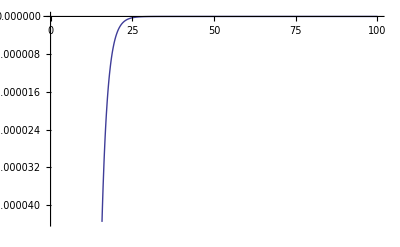

```mathematica
Plot[-ExpIntegralEi[-x]-(-ExpIntegralEi[-x/2]),{x,0,100}]
```

```mathematica
FullSimplify[D[-1+LaguerreL[z,-x]+Hypergeometric1F1[z,1,-x/2]+Integrate[(LaguerreL[z,2u-x]-1)LaguerreL[-z-1,1,-u],{u,0,x/2}],x]]
```

z Hypergeometric1F1[1-z,2,-x]-1/2 z Hypergeometric1F1[1+z,2,-x/2]+∫_0^(x/2) -z^2 Hypergeometric1F1[1-z,2,2 u-x] Hypergeometric1F1[1+z,2,-u]ⅆu

```mathematica
z Hypergeometric1F1[1-z,2,-x]-1/2 z Hypergeometric1F1[1+z,2,-x/2]+∫_0^(x/2) -z^2 Hypergeometric1F1[1-z,2,2 u-x] Hypergeometric1F1[1+z,2,-u]ⅆu/.z->a
```

a Hypergeometric1F1[1-a,2,-x]-1/2 a Hypergeometric1F1[1+a,2,-x/2]+∫_0^(x/2) -a^2 Hypergeometric1F1[1-a,2,2 u-x] Hypergeometric1F1[1+a,2,-u]ⅆu

```mathematica
D[LaguerreL[z,-x],x]
```

LaguerreL[-1+z,1,-x]

```mathematica
Limit[((1+2x)/(1+x))^z,x->Infinity]
```

2^z

```mathematica
D[Integrate[LaguerreL[-z-1,1,-u],{u,0,x}],x]
```

ConditionalExpression[-z Hypergeometric1F1[1+z,2,-x],Re[x]≥-1||x∉Reals]

```mathematica
LaguerreL[-z-1,1,-u]/.u->3/.z->2
```

```mathematica
D[Integrate[LaguerreL[z-1,1,-t],{t,0,2x}],x]
```

2 LaguerreL[-1+z,1,-2 x]

```mathematica
D[Integrate[LaguerreL[z-1,1,-t]LaguerreL[-z-1,1,-u],{t,0,2x},{u,0,x-t/2}],x]
```

∫_0^(2 x) -z^2 Hypergeometric1F1[1-z,2,-t] Hypergeometric1F1[1+z,2,1/2 (t-2 x)]ⅆt

```mathematica
FullSimplify[LaguerreL[-z-1,1,-x]+2 LaguerreL[-1+z,1,-2 x]+∫_0^(2 x) -z^2 Hypergeometric1F1[1-z,2,-t] Hypergeometric1F1[1+z,2,1/2 (t-2 x)]ⅆt]
```

-z Hypergeometric1F1[1+z,2,-x]+∫_0^(2 x) -z^2 Hypergeometric1F1[1-z,2,-t] Hypergeometric1F1[1+z,2,1/2 (t-2 x)]ⅆt+2 LaguerreL[-1+z,1,-2 x]

```mathematica
FullSimplify[-z Hypergeometric1F1[1+z,2,-x]+∫_0^(2 x) -z^2 Hypergeometric1F1[1-z,2,-t] Hypergeometric1F1[1+z,2,1/2 (t-2 x)]ⅆt+2 LaguerreL[-1+z,1,-2 x]/.z->4,Element[x,Integers]]
```

1/6 ⅇ^-x (24+x (6+x)^2)

```mathematica
FullSimplify[D[((1+x)/(1+x/2))^z,x]]
```

2^z (1+x)^(-1+z) (2+x)^(-1-z) z

```mathematica
2^z (1+x)^(-1+z) (2+x)^(-1-z) z/.z->1
```

2/(2+x)^2

```mathematica
FullSimplify[Log[25]/Log[5]]
```

2

```mathematica
Sum[1,{t,2,100},{u,2,(100^(1/2))^(1-Log[100,t])}]
```

44

```mathematica
Sum[1,{t,2,10},{u,2,100/t^2}]
```

44

```mathematica
ba[z_,x_]:=Sum[z^k/k!,{k,0,x}]
```

```mathematica
D[ba[z,0],z]/.z->0
```

0

```mathematica
Product[(1+x/k)^(MoebiusMu[k]/k),{k,1,Infinity}]
```

∏_(k=1)^∞ (1+x/k)^(MoebiusMu[k]/k)

```mathematica
∏_(k=1)^20 (1+x/k)^(MoebiusMu[k]/k)/.x->.5
```

1.25419

```mathematica
bb[x_,r_]:=Product[(1+x/k)^(MoebiusMu[k]/k),{k,1,r}]
bb2[x_,r_]:=Log[Product[(1+x/k)^(MoebiusMu[k]/k),{k,1,r}]]
bb3[x_,r_]:=Sum[(MoebiusMu[k]/k)Log[(1+x/k)],{k,1,r}]
```

```mathematica
Block[{$MaxExtraPrecision=150},N[bb[100000,100000],250]]
```

2.717277784997511242123306219399589709011041619675489980701570161228132643110535094467151277572498488502744424442652999456246944026601360956690204223236126637778975285759860877609975552393373023904710359211011879650736167629673383183187090723869566186

```mathematica
Block[{$MaxExtraPrecision=400},N[bb[1000000,1000000],500]]
```

$Aborted

```mathematica
N@E
```

2.71828

```mathematica
Limit[Product[(1+x/k)^(MoebiusMu[k]/k),{k,1,Infinity}],x->Infinity]
```

```mathematica
1.4422931315820422
```

1.44229

```mathematica
N@Sum[(MoebiusMu[k]/k)Log[(1+1/k)],{k,1,1000000}]
```

0.366235

```mathematica
N[E^-1]
```

0.367879

```mathematica
N[E^(E^-1)]
```

1.44467

```mathematica
FullSimplify[E^(E^-1)]
```

ⅇ^(1/ⅇ)

```mathematica
bb[x_,z_,r_]:=Product[(1+x/k)^(z MoebiusMu[k]/k),{k,1,r}]
```

```mathematica
N[bb[1,2,10000],200]
```

2.0802094774173930577018754490561855175434697604099280043551602652752357289630067594725292768682415175315684403612167747642827643058604752982727257195872876438773846517758644892676018807114523991266594

```mathematica
Log[2.]
```

0.693147

```mathematica
N[(E^(E^-1))]
```

1.44467

```mathematica
Block[{$MaxExtraPrecision=150},N[Product[(1+1/k)^(MoebiusMu[k]/k),{k,1,Infinity}],200]]
```

1.4442614266445797284315890167499989399912986435646138007078686425049221085531112927424762953174290141973351321840639759336326646872774338395852760543025892965993419035215525515504274924647521064283369

```mathematica
Limit[Product[(1/(1-x))^(MoebiusMu[k]/k),{k,1,Infinity}],x->1]
```

1

```mathematica
bb[x_,r_]:=Product[(1+x/k)^(MoebiusMu[k]/k),{k,1,r}]
bob[x_,r_]:=Table[(1+x/k)^(MoebiusMu[k]/k),{k,1,r}]
```

```mathematica
N@bob[100000000,60]
```

{1.×10^8,0.000141421,0.00310723,1.,0.0346572,15.9824,0.0950323,1.,1.,5.01187,0.233023,1.,0.295327,3.08718,2.85054,1.,0.399752,1.,0.442843,1.,2.07965,2.00732,0.514493,1.,1.,1.79172,1.,1.,0.595066,0.606137,0.616657,1.,1.57184,1.54971,1.52917,1.,0.670143,1.47555,1.45993,1.,0.698577,0.704973,0.711117,1.,1.,1.3733,0.733439,1.,1.,1.,1.32856,1.,0.76136,1.,1.29961,1.,1.2869,1.28094,0.78419,1.}

```mathematica
Table[N@bb[10^k,10000],{k,1,10}]
```

$Aborted

```mathematica
bb3[x_,r_]:=Sum[(MoebiusMu[k]/k)Log[1+x/k],{k,1,r}]
bb4[x_,r_]:=Sum[(MoebiusMu[k]/k)(Log[(x+k)]-Log[k]),{k,1,r}]
```

```mathematica
Block[{$MaxExtraPrecision=250},N[bb4[10000,100000],200]]
```

0.99975159479588574114675937270047658026936357415267767363799945819834643250880090448388483133589302997663203347915267030192960061989496037002863493595198175295302187746278573961480067413839281009263162

```mathematica
Block[{$MaxExtraPrecision=350},N[bb4[10000000,1000000],300]]
```

1.00046820283162864711641421991791782485678247199480227149995563172482838958444801737645507196650851757162935300766348254781410571307829588561802324009310074187722670902455490405144176770073710745859705189460916455605766241292781557959580662052160785264488422015393407967159623876213143425390146490962

```mathematica
re[n_]:=Sum[MoebiusMu[k]/k HarmonicNumber[Floor[n/k]],{k,1,n}]
rer[n_,r_]:=Table[MoebiusMu[k]/k HarmonicNumber[Floor[n/k]],{k,1,r}]
rer2[x_,r_]:=Table[(MoebiusMu[k]/k)(Log[1+x/k]),{k,1,r}]
```

```mathematica
re[100000]
```

1

```mathematica
N@rer[100000,10]
```

{12.0901,-5.6985,-3.66384,0.,-2.09615,1.7164,-1.44917,0.,0.,0.978761}

```mathematica
N@rer2[100000,10]
```

{11.5129,-5.4099,-3.47145,0.,-1.98071,1.6202,-1.36673,0.,0.,0.921044}

```mathematica
ec[x_,r_]:=Product[1+x/k,{k,1,r}]
```

```mathematica
N@ec[.1,100000]
```

3.32399

```mathematica
rer3[x_,r_]:=Sum[MoebiusMu[k]/k (-ExpIntegralEi[-x/k]+Log[x/k]+EulerGamma),{k,1,r}]
rer4[x_,r_]:=Sum[MoebiusMu[k]/k (LogIntegral[x^(1/k)]-Log[Log[x^(1/k)]]-EulerGamma),{k,1,r}]
```

```mathematica
N[rer3[100,10000],100]
```

0.9999577624111246857281547836866239317818775664630218061562264706588035990928246079454439478459597893

```mathematica
Block[{$MaxExtraPrecision=250},N[rer4[100,100000],100]]
```

24.66163324347098581782650765663180195916702956757965587250125687275689484849167903168050747973911343

```mathematica
N@RiemannR[100]
```

```mathematica
25.66163326692419
```

```mathematica
D[Sum[MoebiusMu[k]/k (-ExpIntegralEi[-x/k]+Log[x/k]+EulerGamma),{k,1,Infinity}],x]
```

$Aborted

```mathematica
D[(-ExpIntegralEi[-x/k]+Log[x/k]+EulerGamma),x]
```

1/x-ⅇ^(-x/k)/x

```mathematica
Sum[MoebiusMu[k]/k (1/x-ⅇ^(-x/k)/x),{k,1,Infinity}]
```

∑_(k=1)^∞ ((1/x-ⅇ^(-x/k)/x) MoebiusMu[k])/k

```mathematica
D[(LogIntegral[x^(1/k)]-Log[Log[x^(1/k)]]-EulerGamma),x]
```

-1/(k x Log[x^(1/k)])+x^(-1+1/k)/(k Log[x^(1/k)])

```mathematica
Sum[MoebiusMu[k]/k (-1/(k x Log[x^(1/k)])+x^(-1+1/k)/(k Log[x^(1/k)])),{k,1,Infinity}]
```

∑_(k=1)^∞ ((-1/(k x Log[x^(1/k)])+x^(-1+1/k)/(k Log[x^(1/k)])) MoebiusMu[k])/k

```mathematica
Limit[E^z Gamma[x+1,z]/(x!),x->Infinity]
```

ⅇ^z

```mathematica
Sum[z^k/k!,{k,0,x}]
```

(ⅇ^z Gamma[1+x,z])/(x!)

```mathematica
D[(ⅇ^z Gamma[1+x,z])/(x!),z]
```

-z^x/(x!)+(ⅇ^z Gamma[1+x,z])/(x!)

```mathematica
ee[x_,r_]:=Sum[MoebiusMu[k]/k (1/x-ⅇ^(-x/k)/x),{k,1,r}]
```

```mathematica
N[ee[.00000001,100000],100]
```

```mathematica
0.6079271033419373
```

0.607927

```mathematica
1./E
```

0.367879

```mathematica
N[6/Pi^2]
```

0.607927

```mathematica
N[1/Zeta[2]]
```

0.607927

```mathematica
N[ee[1,100000],100]
```

0.3127695771272312989395930855208073513278744057306784247064728826776841022038225270594628409477199342

```mathematica
1./Zeta[4]
```

0.923938

```mathematica
FullSimplify[(1+x)/(1+x/2)]
```

(2 (1+x))/(2+x)

```mathematica
Limit[(2+2x)/(2+x),x->Infinity]
```

2

```mathematica
rp[n_]:=Sum[PrimePi[n^(1/k)]/k,{k,1,Log2@n}]
```

```mathematica
N[rp[1000000000000]-rp[1000000000000/2]]
```

1.82998×10^10

```mathematica
N[HarmonicNumber[1000000000000]-HarmonicNumber[1000000000000/2]]
```

0.693147

```mathematica
N[(-ExpIntegralEi[-1000000000000]+Log[1000000000000]+EulerGamma) - (-ExpIntegralEi[-1000000000000/2]+Log[1000000000000/2]+EulerGamma)]
```

General::unfl: Underflow occurred in computation.

0.693147

```mathematica
Log[2.]
```

0.693147

```mathematica
FullSimplify[(LogIntegral[x]-Log[Log[x]]-EulerGamma)-(LogIntegral[x^(1/2)]-Log[Log[x^(1/2)]]-EulerGamma),Element[x,Integers]]
```

-Log[2]-LogIntegral[√x]+LogIntegral[x]

```mathematica
ea[x_]:=-ExpIntegralEi[-x]+Log[x]+EulerGamma
bea[x_]:=Integrate[(1/Log[t]-1/(t Log[t]))ea[Log[x]/Log[t]],{t,1,x}]
```

```mathematica
N@bea[100.]
```

31.443

```mathematica
LogIntegral[100.]-Log@Log@100-EulerGamma
```

28.0217

```mathematica
LogIntegral[100.]
```

30.1261

```mathematica
Series[(1+x)/(1+x/2),{x,0,10}]
```

1+x/2-x^2/4+x^3/8-x^4/16+x^5/32-x^6/64+x^7/128-x^8/256+x^9/512-x^10/1024+O[x]^11

```mathematica
Series[((1+x)/(1+x/2))^2,{x,0,10}]
```

1+x-x^2/4+x^4/16-x^5/16+(3 x^6)/64-x^7/32+(5 x^8)/256-(3 x^9)/256+(7 x^10)/1024+O[x]^11

```mathematica
Series[((1+x)/(1+x/2))^3,{x,0,10}]
```

1+(3 x)/2-x^3/4+(3 x^4)/16-(3 x^5)/32+x^6/32-(3 x^8)/256+(7 x^9)/512-(3 x^10)/256+O[x]^11

```mathematica
Series[((1+x)/(1+x/2))^-1,{x,0,10}]
```

1-x/2+x^2/2-x^3/2+x^4/2-x^5/2+x^6/2-x^7/2+x^8/2-x^9/2+x^10/2+O[x]^11

```mathematica
1+Sum[(-1)^(k+1) x^k/2^k,{k,1,Infinity}]
```

1+x/(2+x)

```mathematica
((2+x)+x)/(2+x)
```

(2+2 x)/(2+x)

```mathematica
1-Sum[(-x/2)^k,{k,1,Infinity}]
```

1+x/(2+x)

```mathematica
1+Sum[Binomial[z,k](-1)^(k+1) x^k/2^k,{k,1,Infinity}]
```

2-(1-x/2)^z

```mathematica
Sum[Binomial[z,k]Binomial[-z,j]x^k (x/2)^j,{k,0,Infinity},{j,0,Infinity}]
```

2^z ((1+x)/(2+x))^z

```mathematica
Sum[Binomial[z,k]Binomial[-z,j]x^k (y)^j,{k,0,Infinity},{j,0,Infinity}]
```

(1+x)^z (1+y)^-z

```mathematica
Table[Sum[1,{x,1,n},{y,1,n-x}],{n,1,20}]
```

{0,1,3,6,10,15,21,28,36,45,55,66,78,91,105,120,136,153,171,190}

```mathematica
Table[Sum[1,{x,1,n},{y,1,(n-x)/2}],{n,1,20}]
```

{0,0,1,2,4,6,9,12,16,20,25,30,36,42,49,56,64,72,81,90}

```mathematica
1+Integrate[D[(1+t)^z,t],{t,0,x}]+Integrate[D[(1+u)^w,u],{u,0,y}]+Integrate[D[(1+t)^z,t]D[(1+u)^w,u],{t,0,x},{u,0,y}]
```

ConditionalExpression[-1+(1+x)^z+(1+y)^w+(-1+(1+x)^z) (-1+(1+y)^w),(Re[x]≥-1||x∉Reals)&&(Re[y]≥-1||y∉Reals)]

```mathematica
FullSimplify[-1+(1+x)^z+(1+y)^w+(-1+(1+x)^z) (-1+(1+y)^w)]
```

(1+x)^z (1+y)^w

```mathematica
Integrate[D[t^a,t]D[u^b,u],{t,0,x},{u,0,y}]
```

ConditionalExpression[x^a y^b,Re[a]>0]

```mathematica
D[t^a,t]
```

a t^(-1+a)

```mathematica
D[u^b,u]
```

b u^(-1+b)

```mathematica
FullSimplify[Sum[Binomial[u-1,b-1],{u,1,Floor[y(1-t/x)]}],{Element[b,Integers],Element[x,Integers],Element[t,Integers]}]
```

1/b((-1+b) (Binomial[0,-1+b]-Binomial[Floor[y-(t y)/x],-1+b])+Binomial[Floor[y-(t y)/x],-1+b] Floor[y-(t y)/x])

```mathematica
1/(b x)((-1+b) x Binomial[0,-1+b]+(-t y+x (1-b+y)) Binomial[y-(t y)/x,-1+b])
```

```mathematica
(-1+b) x Binomial[0,-1+b]/.b->3
```

0

```mathematica
FullSimplify[((-t y+x (1-b+y)) Binomial[y-(t y)/x,-1+b])/(b x)]
```

((-t y+x (1-b+y)) Binomial[y-(t y)/x,-1+b])/(b x)

```mathematica
FullSimplify@Expand[1/b((-1+b) (-Binomial[Floor[y-(t y)/x],-1+b])+Binomial[Floor[y-(t y)/x],-1+b] Floor[y-(t y)/x])]
```

(Binomial[Floor[y-(t y)/x],-1+b] (1-b+Floor[y-(t y)/x]))/b

```mathematica
Sum[Binomial[u-1,b-1],{u,1,Floor[y(1-t/x)]}]/.t->10/.x->20/.b->3/.y->18
```

84

```mathematica
(Binomial[Floor[y-(t y)/x],-1+b] (1-b+Floor[y-(t y)/x]))/b/.t->10/.x->20/.b->3/.y->18
```

84

```mathematica
(1-b+Floor[y-(t y)/x])/b/.t->10/.x->20/.b->3/.y->18
```

7/3

```mathematica
Binomial[Floor[y-(t y)/x],-1+b]/.t->10/.x->20/.b->3/.y->18
```

36

```mathematica
FullSimplify@Sum[Binomial[u,b],{u,1,f}]
```

((-1+b) Binomial[1,b]+(1-b+f) Binomial[1+f,b])/(1+b)

```mathematica
Integrate[u^(b-1)/(b-1)!,{u,0,y(1-t/x)}]
```

ConditionalExpression[(y-(t y)/x)^b/(b (-1+b)!),Re[b]>0]

```mathematica
Integrate[t^(a-1)/(a-1)! (y-(t y)/x)^b/(b (-1+b)!),{t,0,x}]
```

ConditionalExpression[(x^a y^b)/Gamma[1+a+b],Re[a]>0&&y>0&&Re[b]>-1&&x>0]

```mathematica
Integrate[Log[u]^(b-1)/(b-1)!,{u,1,y^(1-Log[x,t])}]
```

ConditionalExpression[1/((-1+b)!)(Gamma[b]-Gamma[b,-Log[y^(1-Log[t]/Log[x])]]) (-Log[y^(1-Log[t]/Log[x])])^-b Log[y^(1-Log[t]/Log[x])]^b,Re[b]>0]

```mathematica
Integrate[Log[t]^(a-1)/(a-1)! (1/((-1+b)!)(Gamma[b]-Gamma[b,-Log[y^(1-Log[t]/Log[x])]]) (-Log[y^(1-Log[t]/Log[x])])^-b Log[y^(1-Log[t]/Log[x])]^b),{t,1,x}]
```

$Aborted

```mathematica
FullSimplify[1/((-1+b)!)(Gamma[b]-Gamma[b,-Log[y^(1-Log[t]/Log[x])]]) (-Log[y^(1-Log[t]/Log[x])])^-b Log[y^(1-Log[t]/Log[x])]^b,{Element[b,Integers]}]
```

((-1)^b (Gamma[b]-Gamma[b,-Log[y^(1-Log[t]/Log[x])]]))/Gamma[b]

```mathematica
N@(((-1)^b (Gamma[b]-Gamma[b,-Log[y^(1-Log[t]/Log[x])]]))/Gamma[b])/.b->4/.x->10/.y->20/.t->5
```

0.0572838-2.8061×10^-17 ⅈ

```mathematica
N@(((-1)^-b (Gamma[b]-Gamma[b,-(1-Log[t]/Log[x])Log[y]]))/Gamma[b])/.b->4/.x->10/.y->20/.t->5
```

0.0572838+6.16298×10^-33 ⅈ

```mathematica
N@(((-1)^-b (Gamma[b,0,-(1-Log[t]/Log[x])Log[y]]))/Gamma[b])/.b->4/.x->10/.y->20/.t->5
```

0.0572838+6.16298×10^-33 ⅈ

```mathematica
Integrate[Log[t]^(a-1)/(a-1)! (((-1)^-b (Gamma[b,0,-(1-Log[t]/Log[x])Log[y]]))/Gamma[b]),{t,1,x}]
```

∫_1^x ((-1)^-b Gamma[b,0,(-1+Log[t]/Log[x]) Log[y]] Log[t]^(-1+a))/((-1+a)! Gamma[b])ⅆt

```mathematica
Sum[Binomial[u-1,b-1],{u,1,Floor[y(1-t/x)]}]/.t->10/.x->20/.b->3/.y->18
```

84

```mathematica
(Binomial[Floor[y-(t y)/x],-1+b] (1-b+Floor[y-(t y)/x]))/b/.t->10/.x->20/.b->3/.y->18
```

84

```mathematica
Sum[Binomial[t-1,a-1]((Binomial[Floor[y-(t y)/x],-1+b] (1-b+Floor[y-(t y)/x]))/b),{t,1,x}]
```

∑_(t=1)^x 1/b Binomial[-1+t,-1+a] Binomial[Floor[y-(t y)/x],-1+b] (1-b+Floor[y-(t y)/x])

```mathematica
po[x_,y_,a_,b_]:=∑_(t=1)^x 1/b Binomial[-1+t,-1+a] Binomial[Floor[y-(t y)/x],-1+b] (1-b+Floor[y-(t y)/x])
po2[x_,y_,a_,b_]:=Sum[Binomial[t-1,a-1]Binomial[u-1,b-1],{t,1,x},{u,1,y(1-t/x)}]
poa[x_,y_,a_,b_]:=∑_(t=1)^x Binomial[-1+t,-1+a]Binomial[Floor[y(1-t/x)],-1+b] (1-b+Floor[y(1-t/x)])/b
```

```mathematica
poa[32,22,3,4]
```

533916

```mathematica
po2[32,22,3,4]
```

533916

```mathematica
Expand[(1-b+Floor[y(1-t/x)])/b]
```

```mathematica
pex[n_,k_]:=Pochhammer[n,k]/k!
```

```mathematica
Sum[pex[z,t]pex[w,u],{t,0,x},{u,0,Floor[y(1-t/x)]}]
```

$Aborted

```mathematica
FullSimplify[Sum[pex[w,u],{u,0,Floor[y(1-t/x)]}]]
```

Gamma[1+w+Floor[y-(t y)/x]]/(Gamma[1+w] Gamma[1+Floor[y-(t y)/x]])

```mathematica
Gamma[1+w+Floor[y-(t y)/x]]/(Gamma[1+w] Gamma[1+Floor[y-(t y)/x]])/.x->32/.y->22/.t->10/.w->3
```

816

```mathematica
pex[1+Floor[y-(t y)/x],w]/.x->32/.y->22/.t->10/.w->3
```

816

```mathematica
pex[1+w,Floor[y-(t y)/x]]/.x->32/.y->22/.t->10/.w->3
```

816

```mathematica
Sum[pex[z,t]pex[1+Floor[y-(t y)/x],w],{t,0,x}]
```

$Aborted

```mathematica
Sum[pex[z,t]pex[1+w,Floor[y-(t y)/x]],{t,0,x}]
```

∑_(t=0)^x (Pochhammer[1+w,Floor[y-(t y)/x]] Pochhammer[z,t])/(t! Floor[y-(t y)/x]!)

```mathematica
Sum[pex[z,t]pex[1+Floor[y-(t y)/x],w],{t,0,x}]
```

∑_(t=0)^x (Pochhammer[z,t] Pochhammer[1+Floor[y-(t y)/x],w])/(t! w!)

```mathematica
Integrate[LaguerreL[z-1,1,-Log[t]],{t,1,x}]
```

∫_1^x LaguerreL[-1+z,1,-Log[t]]ⅆt

```mathematica
Integrate[LaguerreL[w-1,1,-u],{u,0,y(1-t/x)}]
```

-LaguerreL[w,0]+LaguerreL[w,((t-x) y)/x]

```mathematica
-LaguerreL[w,0]/.w->8
```

-1

```mathematica
FullSimplify[Integrate[LaguerreL[z-1,1,-t](-1+LaguerreL[w,((t-x) y)/x]),{t,0,x}],{Element[x,Integers],Element[y,Integers]}]
```

∫_0^x (-1+LaguerreL[w,(-1+t/x) y]) LaguerreL[-1+z,1,-t]ⅆt

```mathematica
Integrate[1,{t,0,x},{u,0,y(1-t/x)}]
```

(x y)/2

```mathematica
Sum[1,{t,1,x},{u,1,y(1-t/x)}]
```

1/2 (-y+x y)

```mathematica
FullSimplify[1/2 (-y+x y)/.y->x]
```

1/2 (-1+x) x

```mathematica
FullSimplify[Sum[1,{t,1,x},{u,1,y(1-t/x)},{v,1,z(1-t/x-u/y)}]]
```

((-1+x) (-y+x (-3+2 y)) z)/(12 x)

```mathematica
ex[x_]:=Sum[HarmonicNumber[Floor[x/k]],{k,1,x}]
```

```mathematica
Table[ex[n]-ex[n-1],{n,1,10}]
```

{1,3/2,4/3,7/4,6/5,2,8/7,15/8,13/9,9/5}

```mathematica
Table[(ex[n]-ex[n-1])n,{n,1,10}]
```

{1,3,4,7,6,12,8,15,13,18}

```mathematica
Sum[DivisorSigma[1,n]/n,{n,1,10}]
```

7583/504

```mathematica
ex[10]
```

7583/504